```mathematica
vX = Range[6];
vProbability = Table[1/6,{6}];
```

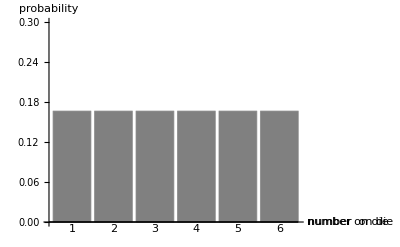

```mathematica
g1=Show[BarChart[vProbability,PlotRange->{Automatic,{0,0.3}},AxesLabel->{"number  on die ","probability "},ChartLabels->vX,BaseStyle->{FontSize->16},ChartStyle->{Gray}],ImagePadding->{{30,100},{30,30}}]
```

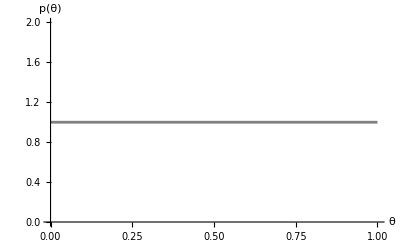

```mathematica
g2 = Show[Plot[PDF[UniformDistribution[{0,1}],θ],{θ,0,1},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{θ,"p(θ)"}],ImagePadding->{{30,100},{30,30}}]
```

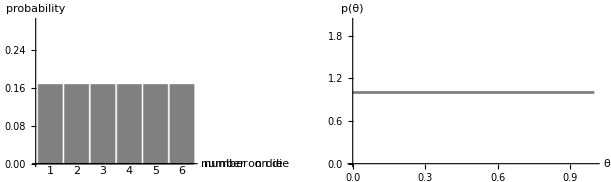

```mathematica
GraphicsRow[{g1,g2}]
```